```mathematica
NotebookDirectory[]
```

/Users/stshammi/temp/graviton_mass_bound/

```mathematica
data=Import[NotebookDirectory[]<>"/graviton_bound_input.csv","CSV"] ;(*m1,m2,beta at 1PN,DL*)
```

```mathematica
Length[data]
```

16332

```mathematica
data[[All,4]]
```

{438.878,614.169,486.951,381.792,539.761,263.405,405.178,531.523,439.966,431.351,434.173,573.033,235.868,463.927,411.62,520.198,353.946,472.7,496.157,362.449,331.046,485.414,16288,667.877,503.853,516.03,471.685,478.006,433.803,439.742,324.81,436.288,507.816,434.641,377.343,324.827,367.651,388.372,494.644,384.585,508.399,382.87,523.184,375.433,432.955}
 |  |  |  |

```mathematica
(*H0=(70*10^5*c)/(10^6*3.261636*tyear)/.{c->3*10^8,tyear->3.1536*10^7}*)
```

```mathematica
(*H0=2.2683085*10^-18*) (*Hubble Constant*)
```

```mathematica
DL=data[[All,4]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,5.46719×10^16,4.52545×10^16,4.43683×10^16,4.46585×10^16,5.89416×10^16,16309,3.88131×10^16,3.34114×10^16,3.78162×10^16,3.99475×10^16,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

We want to write redshift z in terms of luminosity distance DL following Eq. 2.16 of 0411129, since LIGO data gives us DL

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,0.0956385,0.0938834,0.0944587,0.122241,0.0528873,16306,0.109319,0.0945542,0.0827856,0.0718314,0.0807763,0.0850656,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
Dα=z2/(2.2683085*10^-18*Sqrt[ωM+ωΛ])(1-(z2/4*(3ωM)/(ωM+ωΛ)+2α))/.{ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18} (*Eq.25 of 1603.08955. matter and dark energy denisties are taken from 1807.06209, table2*)
```

{4.11288×10^16,5.56899×10^16,4.5214×10^16,3.61818×10^16,4.96202×10^16,2.55691×10^16,3.82212×10^16,4.89383×10^16,4.12221×10^16,4.04825×10^16,4.0725×10^16,16310,3.57917×10^16,3.11366×10^16,3.49397×10^16,3.67574×10^16,4.58611×10^16,3.64263×10^16,4.70136×10^16,3.62761×10^16,4.82461×10^16,3.5624×10^16,4.06204×10^16}
 |  |  |  |

```mathematica
ℳ=(data[[All,1]]*tsolar*data[[All,2]]*tsolar)^(3/5)/(data[[All,1]]*tsolar+data[[All,2]]*tsolar)^(1/5)/.tsolar->4.925491*10^-6 (*Chirp Mass*)
```

{0.000151738,0.000158306,0.000151815,0.000156996,0.000151988,0.000152425,0.000161415,0.000150048,0.000153011,0.000146153,0.000151112,16310,0.000152348,0.000153956,0.000152612,0.000155839,0.000151118,0.00015464,0.000152945,0.000152474,0.000154203,0.000153984,0.000158831}
 |  |  |  |

```mathematica
(*λGeo=√(π^2/(data[[All,3]]/1.64485)*Dα *ℳ/(1+z2))(*wavelength in geometric units*)*)
```

```mathematica
(*λ=λGeo*3*10^8(*wavelength in meters*)*)
```

```mathematica
σβ=data[[All,3]]/1.64485 (*1- sigma upper bound on  \[beta*)
```

{0.0190899,0.0200018,0.019637,0.0196978,0.0192115,0.0207314,0.0201234,0.0192723,0.0192723,0.0181172,0.0190291,0.0189683,16308,0.019637,0.0194547,0.0200018,0.0195155,0.020245,0.0194547,0.0198802,0.019637,0.0193939,0.0203666,0.0206098,0.020245}
 |  |  |  |

```mathematica
funβ[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
funβ2[x_,y_]=1/(√(2*π)*y)*Exp[-x^2/(2 y^2)]  (* x is \[beta and y is sigma-\[beta*)
```

(ⅇ^(-x^2/(2 y^2)))/(√(2 π) y)

```mathematica
Const1=(π^2 Dα *ℳ)/(1+z2)
```

{5.62291×10^13,7.69815×10^13,6.13015×10^13,5.17327×10^13,6.67159×10^13,3.63292×10^13,5.59383×10^13,6.50544×10^13,5.6818×10^13,5.33831×10^13,5.54959×10^13,6.88801×10^13,16309,4.97021×10^13,4.41409×10^13,4.86936×10^13,5.21033×10^13,6.18068×10^13,5.12735×10^13,6.3967×10^13,5.03635×10^13,6.60087×10^13,5.0019×10^13,5.81941×10^13}
 |  |  |  |

```mathematica
Subscript[σ, ρ]=10^16*σβ/Const1 (*ρ=10^16/λGeo^2. I chose this because ρ is proportional to β and hence we know that the distribution is going to be Gaussian. I multiplied by 10^16 because otherwise the number is too small and mathematica does not give desired accuracy *)
```

{3.39502,2.59826,3.20335,3.80762,2.8796,5.70653,3.59743,2.96249,3.39193,3.3938,3.42892,2.75381,5.99721,3.26746,16304,3.50397,3.00174,3.47089,3.91425,4.53136,4.00781,3.88555,3.14766,3.87729,3.06987,3.85078,3.08544,4.12039,3.47888}
 |  |  |  |

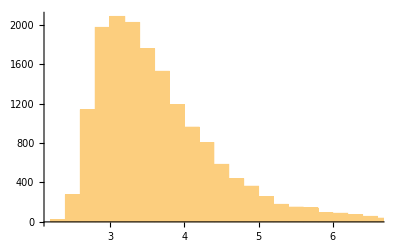

```mathematica
Histogram[Subscript[σ, ρ]]
```

```mathematica
Subscript[Maxσ, ρ]=Max[Subscript[σ, ρ]]
```

10.2248

```mathematica
Subscript[Minσ, ρ]=Min[Subscript[σ, ρ]]
```

2.26711

```mathematica
Subscript[𝒟logσ, ρ]=HistogramDistribution[Subscript[σ, ρ]]
```

DataDistribution[…]

```mathematica
Subscript[pslogσ, ρ]=PDF[Subscript[𝒟logσ, ρ],x];
```

```mathematica
funβ2[x_,y_]=1/(√(2*π)*y)*Exp[-x^2/(2 y^2)]
```

(ⅇ^(-x^2/(2 y^2)))/(√(2 π) y)

```mathematica
σρSampleLog=Prepend[10^Range[-1,1.31,0.01],0]
```

{0,0.1,0.102329,0.104713,0.107152,0.109648,0.112202,0.114815,0.11749,0.120226,0.123027,0.125893,0.128825,0.131826,0.134896,0.138038,0.141254,0.144544,0.147911,0.151356,0.154882,0.158489,0.162181,0.165959,0.169824,0.17378,0.177828,0.18197,0.186209,0.190546,0.194984,0.199526,0.204174,0.20893,0.213796,0.218776,0.223872,0.229087,0.234423,0.239883,0.245471,0.251189,0.25704,0.263027,0.269153,0.275423,0.281838,0.288403,0.295121,0.301995,0.30903,0.316228,0.323594,0.331131,0.338844,0.346737,0.354813,0.363078,0.371535,0.380189,0.389045,0.398107,0.40738,0.416869,0.42658,0.436516,0.446684,0.457088,0.467735,0.47863,0.489779,0.501187,0.512861,0.524807,0.537032,0.549541,0.562341,0.57544,0.588844,0.60256,0.616595,0.630957,0.645654,0.660693,0.676083,0.691831,0.707946,0.724436,0.74131,0.758578,0.776247,0.794328,0.812831,0.831764,0.851138,0.870964,0.891251,0.912011,0.933254,0.954993,0.977237,1.,1.02329,1.04713,1.07152,1.09648,1.12202,1.14815,1.1749,1.20226,1.23027,1.25893,1.28825,1.31826,1.34896,1.38038,1.41254,1.44544,1.47911,1.51356,1.54882,1.58489,1.62181,1.65959,1.69824,1.7378,1.77828,1.8197,1.86209,1.90546,1.94984,1.99526,2.04174,2.0893,2.13796,2.18776,2.23872,2.29087,2.34423,2.39883,2.45471,2.51189,2.5704,2.63027,2.69153,2.75423,2.81838,2.88403,2.95121,3.01995,3.0903,3.16228,3.23594,3.31131,3.38844,3.46737,3.54813,3.63078,3.71535,3.80189,3.89045,3.98107,4.0738,4.16869,4.2658,4.36516,4.46684,4.57088,4.67735,4.7863,4.89779,5.01187,5.12861,5.24807,5.37032,5.49541,5.62341,5.7544,5.88844,6.0256,6.16595,6.30957,6.45654,6.60693,6.76083,6.91831,7.07946,7.24436,7.4131,7.58578,7.76247,7.94328,8.12831,8.31764,8.51138,8.70964,8.91251,9.12011,9.33254,9.54993,9.77237,10.,10.2329,10.4713,10.7152,10.9648,11.2202,11.4815,11.749,12.0226,12.3027,12.5893,12.8825,13.1826,13.4896,13.8038,14.1254,14.4544,14.7911,15.1356,15.4882,15.8489,16.2181,16.5959,16.9824,17.378,17.7828,18.197,18.6209,19.0546,19.4984,19.9526,20.4174}

```mathematica
fun1σρTable[y_]=Table[{σρSampleLog[[i]],funβ2[σρSampleLog[[i]],y]},{i,1,Length[σρSampleLog]}]; (*fun1[x_,y_]*)
```

```mathematica
σρMC[x_]=Subscript[pslogσ, ρ];
```

```mathematica
σρMC[2]
```

0.

```mathematica
σρMC[10]
```

0.

```mathematica
σρMCSample=Range[0,20,0.5]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.}

```mathematica
σρMCTable=Table[{σρMCSample[[i]],σρMC[σρMCSample[[i]]]},{i,1,Length[σρMCSample]}]
```

{{0.,0.},{0.5,0.},{1.,0.},{1.5,0.},{2.,0.},{2.5,0.0838844},{3.,0.638317},{3.5,0.537289},{4.,0.29482},{4.5,0.17879},{5.,0.0783737},{5.5,0.0462283},{6.,0.026941},{6.5,0.0171443},{7.,0.00397992},{7.5,0.00459221},{8.,0.00214303},{8.5,0.00153074},{9.,0.000306147},{9.5,0.000918442},{10.,0.},{10.5,0.},{11.,0.},{11.5,0.},{12.,0.},{12.5,0.},{13.,0.},{13.5,0.},{14.,0.},{14.5,0.},{15.,0.},{15.5,0.},{16.,0.},{16.5,0.},{17.,0.},{17.5,0.},{18.,0.},{18.5,0.},{19.,0.},{19.5,0.},{20.,0.}}

```mathematica
σρMCTableInterp=Interpolation[σρMCTable]
```

InterpolatingFunction[…]

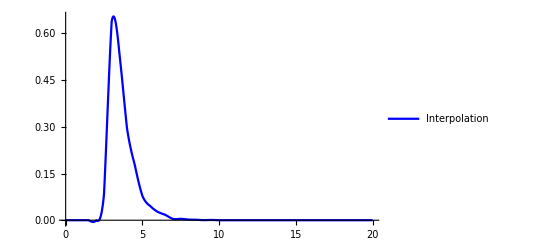

```mathematica
plotσρMCTableInterp=Plot[σρMCTableInterp[x],{x,0,20},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

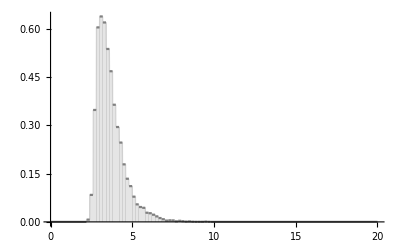

```mathematica
plot1=Plot[σρMC[x],{x,0,20},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

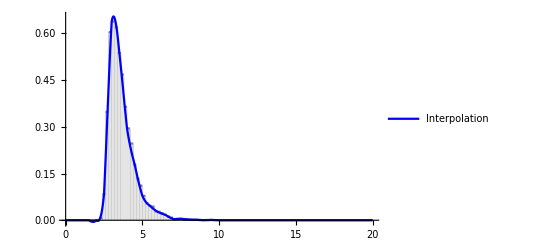

```mathematica
Show[plot1,plotσρMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
ρFinalPDF=Table[{fun1σρTable[y][[i,1]],NIntegrate[fun1σρTable[y][[i,2]]*σρMCTableInterp[y],{y,0,20}]},{i,1,Length[fun1σρTable[y]]}]
```

{{0,0.108935},{0.1,0.108886},{0.102329,0.108884},{0.104713,0.108881},{0.107152,0.108879},{0.109648,0.108876},{0.112202,0.108873},{0.114815,0.10887},{0.11749,0.108867},{0.120226,0.108864},{0.123027,0.108861},{0.125893,0.108857},{0.128825,0.108854},{0.131826,0.10885},{0.134896,0.108846},{0.138038,0.108842},{0.141254,0.108837},{0.144544,0.108833},{0.147911,0.108828},{0.151356,0.108823},{0.154882,0.108817},{0.158489,0.108812},{0.162181,0.108806},{0.165959,0.1088},{0.169824,0.108794},{0.17378,0.108787},{0.177828,0.10878},{0.18197,0.108773},{0.186209,0.108765},{0.190546,0.108757},{0.194984,0.108749},{0.199526,0.10874},{0.204174,0.108731},{0.20893,0.108722},{0.213796,0.108711},{0.218776,0.108701},{0.223872,0.10869},{0.229087,0.108678},{0.234423,0.108666},{0.239883,0.108654},{0.245471,0.108641},{0.251189,0.108627},{0.25704,0.108612},{0.263027,0.108597},{0.269153,0.108581},{0.275423,0.108565},{0.281838,0.108547},{0.288403,0.108529},{0.295121,0.10851},{0.301995,0.10849},{0.30903,0.108469},{0.316228,0.108447},{0.323594,0.108424},{0.331131,0.1084},{0.338844,0.108375},{0.346737,0.108349},{0.354813,0.108321},{0.363078,0.108292},{0.371535,0.108262},{0.380189,0.108231},{0.389045,0.108198},{0.398107,0.108163},{0.40738,0.108127},{0.416869,0.108089},{0.42658,0.108049},{0.436516,0.108008},{0.446684,0.107964},{0.457088,0.107919},{0.467735,0.107871},{0.47863,0.107821},{0.489779,0.107769},{0.501187,0.107714},{0.512861,0.107657},{0.524807,0.107597},{0.537032,0.107535},{0.549541,0.107469},{0.562341,0.107401},{0.57544,0.107329},{0.588844,0.107254},{0.60256,0.107175},{0.616595,0.107093},{0.630957,0.107007},{0.645654,0.106918},{0.660693,0.106823},{0.676083,0.106725},{0.691831,0.106622},{0.707946,0.106514},{0.724436,0.106402},{0.74131,0.106284},{0.758578,0.106161},{0.776247,0.106032},{0.794328,0.105897},{0.812831,0.105757},{0.831764,0.105609},{0.851138,0.105455},{0.870964,0.105294},{0.891251,0.105126},{0.912011,0.10495},{0.933254,0.104767},{0.954993,0.104574},{0.977237,0.104374},{1.,0.104164},{1.02329,0.103945},{1.04713,0.103716},{1.07152,0.103477},{1.09648,0.103227},{1.12202,0.102966},{1.14815,0.102694},{1.1749,0.10241},{1.20226,0.102113},{1.23027,0.101803},{1.25893,0.10148},{1.28825,0.101143},{1.31826,0.100791},{1.34896,0.100424},{1.38038,0.100041},{1.41254,0.0996419},{1.44544,0.0992259},{1.47911,0.0987924},{1.51356,0.0983406},{1.54882,0.09787},{1.58489,0.0973798},{1.62181,0.0968695},{1.65959,0.0963382},{1.69824,0.0957853},{1.7378,0.0952101},{1.77828,0.0946119},{1.8197,0.0939899},{1.86209,0.0933434},{1.90546,0.0926717},{1.94984,0.091974},{1.99526,0.0912497},{2.04174,0.0904979},{2.0893,0.0897181},{2.13796,0.0889094},{2.18776,0.0880713},{2.23872,0.0872029},{2.29087,0.0863038},{2.34423,0.0853733},{2.39883,0.0844108},{2.45471,0.0834159},{2.51189,0.0823879},{2.5704,0.0813265},{2.63027,0.0802313},{2.69153,0.079102},{2.75423,0.0779384},{2.81838,0.0767403},{2.88403,0.0755076},{2.95121,0.0742403},{3.01995,0.0729387},{3.0903,0.0716029},{3.16228,0.0702333},{3.23594,0.0688304},{3.31131,0.0673949},{3.38844,0.0659274},{3.46737,0.0644289},{3.54813,0.0629006},{3.63078,0.0613436},{3.71535,0.0597593},{3.80189,0.0581494},{3.89045,0.0565156},{3.98107,0.0548598},{4.0738,0.0531843},{4.16869,0.0514912},{4.2658,0.0497831},{4.36516,0.0480627},{4.46684,0.0463327},{4.57088,0.0445962},{4.67735,0.0428563},{4.7863,0.0411163},{4.89779,0.0393795},{5.01187,0.0376494},{5.12861,0.0359297},{5.24807,0.034224},{5.37032,0.0325359},{5.49541,0.0308691},{5.62341,0.0292273},{5.7544,0.0276141},{5.88844,0.026033},{6.0256,0.0244874},{6.16595,0.0229806},{6.30957,0.0215156},{6.45654,0.0200954},{6.60693,0.0187227},{6.76083,0.0173997},{6.91831,0.0161286},{7.07946,0.0149112},{7.24436,0.013749},{7.4131,0.012643},{7.58578,0.011594},{7.76247,0.0106025},{7.94328,0.00966847},{8.12831,0.00879171},{8.31764,0.00797157},{8.51138,0.00720713},{8.70964,0.00649715},{8.91251,0.00584014},{9.12011,0.00523432},{9.33254,0.00467775},{9.54993,0.00416828},{9.77237,0.00370359},{10.,0.00328129},{10.2329,0.00289888},{10.4713,0.00255381},{10.7152,0.00224353},{10.9648,0.00196551},{11.2202,0.00171722},{11.4815,0.00149625},{11.749,0.00130022},{12.0226,0.0011269},{12.3027,0.000974118},{12.5893,0.000839872},{12.8825,0.000722269},{13.1826,0.00061955},{13.4896,0.000530093},{13.8038,0.000452408},{14.1254,0.000385134},{14.4544,0.000327036},{14.7911,0.000277},{15.1356,0.000234021},{15.4882,0.000197204},{15.8489,0.000165747},{16.2181,0.000138942},{16.5959,0.00011616},{16.9824,0.0000968502},{17.378,0.0000805263},{17.7828,0.0000667642},{18.197,0.0000551937},{18.6209,0.000045493},{19.0546,0.0000373831},{19.4984,0.0000306229},{19.9526,0.0000250046},{20.4174,0.0000203495}}

```mathematica
ρFinalPDFInterp=Interpolation[ρFinalPDF]
```

InterpolatingFunction[…]

```mathematica
ρNormalization=NIntegrate[ρFinalPDFInterp[x],{x,0,Max[Subscript[σ, ρ]]}]
```

0.473186

```mathematica
ρFinalPDFNorm=Table[{ρFinalPDF[[i,1]],ρFinalPDF[[i,2]]/ρNormalization},{i,1,Length[ρFinalPDF]}];
```

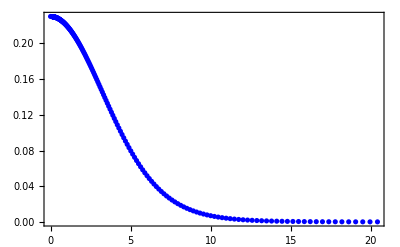

```mathematica
plotρFinalPDFNorm=ListPlot[{ρFinalPDFNorm},PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ρFinalPDFNormInterp=Interpolation[ρFinalPDFNorm]
```

InterpolatingFunction[…]

```mathematica
ρFinalCDFNorm=Table[{σρSampleLog[[i]],NIntegrate[ρFinalPDFNormInterp[x],{x,0,σρSampleLog[[i]]}]},{i,1,Length[σρSampleLog]}]
```

{{0,0},{0.1,0.0230181},{0.102329,0.0235541},{0.104713,0.0241026},{0.107152,0.0246638},{0.109648,0.0252381},{0.112202,0.0258257},{0.114815,0.0264271},{0.11749,0.0270424},{0.120226,0.027672},{0.123027,0.0283163},{0.125893,0.0289755},{0.128825,0.0296501},{0.131826,0.0303404},{0.134896,0.0310468},{0.138038,0.0317695},{0.141254,0.0325091},{0.144544,0.0332659},{0.147911,0.0340402},{0.151356,0.0348326},{0.154882,0.0356434},{0.158489,0.036473},{0.162181,0.0373219},{0.165959,0.0381905},{0.169824,0.0390793},{0.17378,0.0399888},{0.177828,0.0409194},{0.18197,0.0418716},{0.186209,0.0428459},{0.190546,0.0438428},{0.194984,0.0448629},{0.199526,0.0459067},{0.204174,0.0469747},{0.20893,0.0480674},{0.213796,0.0491856},{0.218776,0.0503296},{0.223872,0.0515002},{0.229087,0.0526979},{0.234423,0.0539234},{0.239883,0.0551773},{0.245471,0.0564603},{0.251189,0.057773},{0.25704,0.0591161},{0.263027,0.0604902},{0.269153,0.0618962},{0.275423,0.0633347},{0.281838,0.0648065},{0.288403,0.0663124},{0.295121,0.067853},{0.301995,0.0694292},{0.30903,0.0710419},{0.316228,0.0726918},{0.323594,0.0743798},{0.331131,0.0761067},{0.338844,0.0778734},{0.346737,0.0796809},{0.354813,0.08153},{0.363078,0.0834217},{0.371535,0.0853569},{0.380189,0.0873366},{0.389045,0.0893619},{0.398107,0.0914336},{0.40738,0.093553},{0.416869,0.0957209},{0.42658,0.0979386},{0.436516,0.100207},{0.446684,0.102527},{0.457088,0.104901},{0.467735,0.107329},{0.47863,0.109812},{0.489779,0.112351},{0.501187,0.114949},{0.512861,0.117606},{0.524807,0.120323},{0.537032,0.123102},{0.549541,0.125944},{0.562341,0.12885},{0.57544,0.131822},{0.588844,0.134861},{0.60256,0.137969},{0.616595,0.141147},{0.630957,0.144396},{0.645654,0.147718},{0.660693,0.151115},{0.676083,0.154588},{0.691831,0.158138},{0.707946,0.161767},{0.724436,0.165477},{0.74131,0.169269},{0.758578,0.173146},{0.776247,0.177108},{0.794328,0.181157},{0.812831,0.185295},{0.831764,0.189523},{0.851138,0.193844},{0.870964,0.198259},{0.891251,0.20277},{0.912011,0.207378},{0.933254,0.212086},{0.954993,0.216895},{0.977237,0.221806},{1.,0.226822},{1.02329,0.231944},{1.04713,0.237174},{1.07152,0.242514},{1.09648,0.247966},{1.12202,0.25353},{1.14815,0.25921},{1.1749,0.265006},{1.20226,0.27092},{1.23027,0.276955},{1.25893,0.28311},{1.28825,0.289389},{1.31826,0.295791},{1.34896,0.30232},{1.38038,0.308976},{1.41254,0.31576},{1.44544,0.322674},{1.47911,0.329719},{1.51356,0.336896},{1.54882,0.344205},{1.58489,0.351649},{1.62181,0.359226},{1.65959,0.366939},{1.69824,0.374786},{1.7378,0.38277},{1.77828,0.390889},{1.8197,0.399144},{1.86209,0.407534},{1.90546,0.41606},{1.94984,0.424719},{1.99526,0.433513},{2.04174,0.442438},{2.0893,0.451495},{2.13796,0.460681},{2.18776,0.469994},{2.23872,0.479432},{2.29087,0.488992},{2.34423,0.498673},{2.39883,0.508469},{2.45471,0.518378},{2.51189,0.528395},{2.5704,0.538517},{2.63027,0.548738},{2.69153,0.559053},{2.75423,0.569457},{2.81838,0.579943},{2.88403,0.590504},{2.95121,0.601134},{3.01995,0.611824},{3.0903,0.622568},{3.16228,0.633357},{3.23594,0.64418},{3.31131,0.65503},{3.38844,0.665896},{3.46737,0.676768},{3.54813,0.687634},{3.63078,0.698484},{3.71535,0.709306},{3.80189,0.720088},{3.89045,0.730818},{3.98107,0.741483},{4.0738,0.752069},{4.16869,0.762564},{4.2658,0.772955},{4.36516,0.783228},{4.46684,0.793369},{4.57088,0.803365},{4.67735,0.813203},{4.7863,0.82287},{4.89779,0.832351},{5.01187,0.841636},{5.12861,0.850712},{5.24807,0.859566},{5.37032,0.868188},{5.49541,0.876568},{5.62341,0.884695},{5.7544,0.892561},{5.88844,0.900157},{6.0256,0.907477},{6.16595,0.914515},{6.30957,0.921266},{6.45654,0.927726},{6.60693,0.933893},{6.76083,0.939765},{6.91831,0.945342},{7.07946,0.950625},{7.24436,0.955616},{7.4131,0.96032},{7.58578,0.96474},{7.76247,0.968881},{7.94328,0.972752},{8.12831,0.976358},{8.31764,0.979709},{8.51138,0.982814},{8.70964,0.985683},{8.91251,0.988325},{9.12011,0.990752},{9.33254,0.992975},{9.54993,0.995005},{9.77237,0.996853},{10.,0.998531},{10.2329,1.00005},{10.4713,1.00142},{10.7152,1.00266},{10.9648,1.00376},{11.2202,1.00476},{11.4815,1.00564},{11.749,1.00643},{12.0226,1.00713},{12.3027,1.00775},{12.5893,1.0083},{12.8825,1.00878},{13.1826,1.00921},{13.4896,1.00958},{13.8038,1.00991},{14.1254,1.01019},{14.4544,1.01044},{14.7911,1.01065},{15.1356,1.01084},{15.4882,1.011},{15.8489,1.01114},{16.2181,1.01125},{16.5959,1.01136},{16.9824,1.01144},{17.378,1.01152},{17.7828,1.01158},{18.197,1.01163},{18.6209,1.01168},{19.0546,1.01172},{19.4984,1.01175},{19.9526,1.01177},{20.4174,1.0118}}

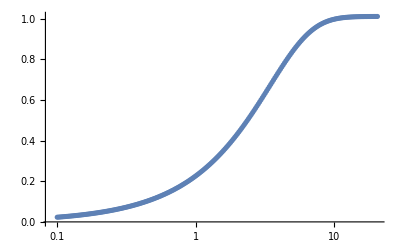

```mathematica
ListLogLinearPlot[ρFinalCDFNorm,PlotRange->All]
```

```mathematica
ρFinalCDFNormInterp=Interpolation[ρFinalCDFNorm]
```

InterpolatingFunction[…]

```mathematica
ρ90CL=x/.FindRoot[ρFinalCDFNormInterp[x]==0.9,{x,4}]
```

5.88558

```mathematica
(ρ90CL/10^16)^(-1/2)*3*10^5 (*A rough estimate of graviton wavelength in km*)
```

1.23659×10^13

```mathematica
(Max[σβ]/const1)^(-1/2)*3*10^5
```

(1.96858×10^6)/(√(1/const1))

```mathematica
(Min[σβ]/const1)^(-1/2)*3*10^5
```

(2.40004×10^6)/(√(1/const1))

```mathematica
ρSample=10^Range[-3.9,1.39254,0.1]
```

{0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526}

We want to find pdf of λ from pdf of ρ

```mathematica
λSample=(10^16/ρSample)^(1/2)
```

{8.91251×10^9,7.94328×10^9,7.07946×10^9,6.30957×10^9,5.62341×10^9,5.01187×10^9,4.46684×10^9,3.98107×10^9,3.54813×10^9,3.16228×10^9,2.81838×10^9,2.51189×10^9,2.23872×10^9,1.99526×10^9,1.77828×10^9,1.58489×10^9,1.41254×10^9,1.25893×10^9,1.12202×10^9,1.×10^9,8.91251×10^8,7.94328×10^8,7.07946×10^8,6.30957×10^8,5.62341×10^8,5.01187×10^8,4.46684×10^8,3.98107×10^8,3.54813×10^8,3.16228×10^8,2.81838×10^8,2.51189×10^8,2.23872×10^8,1.99526×10^8,1.77828×10^8,1.58489×10^8,1.41254×10^8,1.25893×10^8,1.12202×10^8,1.×10^8,8.91251×10^7,7.94328×10^7,7.07946×10^7,6.30957×10^7,5.62341×10^7,5.01187×10^7,4.46684×10^7,3.98107×10^7,3.54813×10^7,3.16228×10^7,2.81838×10^7,2.51189×10^7,2.23872×10^7}

```mathematica
pdfλtable1=Table[{λSample[[i]]*3*10^5,(2*10^16)/λSample[[i]]^3*ρFinalPDFNormInterp[10^16/λSample[[i]]^2]},{i,1,Length[λSample]}](*pdf of λ where λ is in km *)
```

{{2.67375×10^15,6.50376×10^-15},{2.38298×10^15,9.1868×10^-15},{2.12384×10^15,1.29767×10^-14},{1.89287×10^15,1.83301×10^-14},{1.68702×10^15,2.58919×10^-14},{1.50356×10^15,3.65733×10^-14},{1.34005×10^15,5.16612×10^-14},{1.19432×10^15,7.29734×10^-14},{1.06444×10^15,1.03078×10^-13},{9.48683×10^14,1.45601×10^-13},{8.45515×10^14,2.05667×10^-13},{7.53566×10^14,2.90512×10^-13},{6.71616×10^14,4.10359×10^-13},{5.98579×10^14,5.79648×10^-13},{5.33484×10^14,8.18774×10^-13},{4.75468×10^14,1.15655×10^-12},{4.23761×10^14,1.63367×10^-12},{3.77678×10^14,2.30762×10^-12},{3.36606×10^14,3.25959×10^-12},{3.×10^14,4.60429×10^-12},{2.67375×10^14,6.50371×10^-12},{2.38298×10^14,9.1867×10^-12},{2.12384×10^14,1.29765×10^-11},{1.89287×10^14,1.83296×10^-11},{1.68702×10^14,2.58908×10^-11},{1.50356×10^14,3.65707×10^-11},{1.34005×10^14,5.16554×10^-11},{1.19432×10^14,7.29603×10^-11},{1.06444×10^14,1.03048×10^-10},{9.48683×10^13,1.45536×10^-10},{8.45515×10^13,2.05521×10^-10},{7.53566×10^13,2.90185×10^-10},{6.71616×10^13,4.09627×10^-10},{5.98579×10^13,5.78009×10^-10},{5.33484×10^13,8.1511×10^-10},{4.75468×10^13,1.14836×10^-9},{4.23761×10^13,1.61537×10^-9},{3.77678×10^13,2.26679×10^-9},{3.36606×10^13,3.16872×10^-9},{3.×10^13,4.40267×10^-9},{2.67375×10^13,6.05868×10^-9},{2.38298×10^13,8.21235×10^-9},{2.12384×10^13,1.087×10^-8},{1.89287×10^13,1.38631×10^-8},{1.68702×10^13,1.66933×10^-8},{1.50356×10^13,1.84184×10^-8},{1.34005×10^13,1.78549×10^-8},{1.19432×10^13,1.44129×10^-8},{1.06444×10^13,9.14863×10^-9},{9.48683×10^12,4.38574×10^-9},{8.45515×10^12,1.58567×10^-9},{7.53566×10^12,4.42022×10^-10},{6.71616×10^12,9.41929×10^-11}}

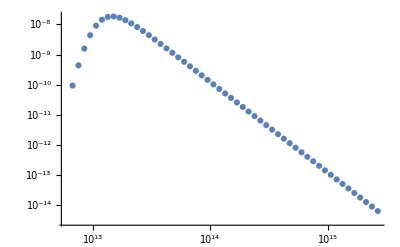

```mathematica
ListLogLogPlot[pdfλtable1]
```

```mathematica
λFinalPDFInterp=Interpolation[pdfλtable1]
```

InterpolatingFunction[…]

```mathematica
λNormalization=NIntegrate[λFinalPDFInterp[x],{x,Min[λSample]*3*10^5,Max[λSample]*3*10^5}]
```

303505.

```mathematica
λFinalPDFNorm=Table[{pdfλtable1[[i,1]],pdfλtable1[[i,2]]/λNormalization},{i,1,Length[pdfλtable1]}]
```

{{2.67375×10^15,2.14289×10^-20},{2.38298×10^15,3.02691×10^-20},{2.12384×10^15,4.27562×10^-20},{1.89287×10^15,6.03947×10^-20},{1.68702×10^15,8.53098×10^-20},{1.50356×10^15,1.20503×10^-19},{1.34005×10^15,1.70215×10^-19},{1.19432×10^15,2.40436×10^-19},{1.06444×10^15,3.39624×10^-19},{9.48683×10^14,4.79732×10^-19},{8.45515×10^14,6.7764×10^-19},{7.53566×10^14,9.57192×10^-19},{6.71616×10^14,1.35207×10^-18},{5.98579×10^14,1.90985×10^-18},{5.33484×10^14,2.69773×10^-18},{4.75468×10^14,3.81065×10^-18},{4.23761×10^14,5.38268×10^-18},{3.77678×10^14,7.60323×10^-18},{3.36606×10^14,1.07398×10^-17},{3.×10^14,1.51704×10^-17},{2.67375×10^14,2.14287×10^-17},{2.38298×10^14,3.02687×10^-17},{2.12384×10^14,4.27554×10^-17},{1.89287×10^14,6.0393×10^-17},{1.68702×10^14,8.5306×10^-17},{1.50356×10^14,1.20495×10^-16},{1.34005×10^14,1.70196×10^-16},{1.19432×10^14,2.40393×10^-16},{1.06444×10^14,3.39528×10^-16},{9.48683×10^13,4.79517×10^-16},{8.45515×10^13,6.77158×10^-16},{7.53566×10^13,9.56113×10^-16},{6.71616×10^13,1.34966×10^-15},{5.98579×10^13,1.90445×10^-15},{5.33484×10^13,2.68566×10^-15},{4.75468×10^13,3.78365×10^-15},{4.23761×10^13,5.32238×10^-15},{3.77678×10^13,7.46873×10^-15},{3.36606×10^13,1.04404×10^-14},{3.×10^13,1.45061×10^-14},{2.67375×10^13,1.99624×10^-14},{2.38298×10^13,2.70584×10^-14},{2.12384×10^13,3.58149×10^-14},{1.89287×10^13,4.56768×10^-14},{1.68702×10^13,5.50017×10^-14},{1.50356×10^13,6.06858×10^-14},{1.34005×10^13,5.8829×10^-14},{1.19432×10^13,4.74883×10^-14},{1.06444×10^13,3.01433×10^-14},{9.48683×10^12,1.44503×10^-14},{8.45515×10^12,5.22452×10^-15},{7.53566×10^12,1.45639×10^-15},{6.71616×10^12,3.10351×10^-16}}

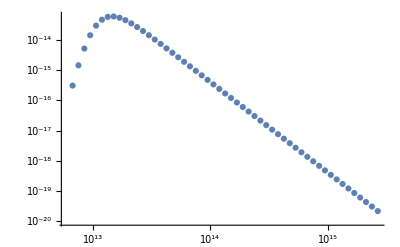

```mathematica
ListLogLogPlot[λFinalPDFNorm]
```

```mathematica
λFinalPDFNormInterp=Interpolation[λFinalPDFNorm]
```

InterpolatingFunction[…]

```mathematica
λFinalCDFNorm=Table[{λSample[[i]]*3*10^5,NIntegrate[λFinalPDFNormInterp[x],{x,Min[λSample]*3*10^5,3*10^5*λSample[[i]]}]},{i,1,Length[λSample]}]
```

{{2.67375×10^15,1.},{2.38298×10^15,0.999993},{2.12384×10^15,0.999983},{1.89287×10^15,0.999971},{1.68702×10^15,0.999957},{1.50356×10^15,0.999938},{1.34005×10^15,0.999915},{1.19432×10^15,0.999885},{1.06444×10^15,0.999848},{9.48683×10^14,0.999801},{8.45515×10^14,0.999742},{7.53566×10^14,0.999668},{6.71616×10^14,0.999575},{5.98579×10^14,0.999458},{5.33484×10^14,0.99931},{4.75468×10^14,0.999124},{4.23761×10^14,0.998889},{3.77678×10^14,0.998594},{3.36606×10^14,0.998223},{3.×10^14,0.997755},{2.67375×10^14,0.997167},{2.38298×10^14,0.996426},{2.12384×10^14,0.995493},{1.89287×10^14,0.994318},{1.68702×10^14,0.99284},{1.50356×10^14,0.990979},{1.34005×10^14,0.988635},{1.19432×10^14,0.985686},{1.06444×10^14,0.981973},{9.48683×10^13,0.977299},{8.45515×10^13,0.971416},{7.53566×10^13,0.964012},{6.71616×10^13,0.954696},{5.98579×10^13,0.942978},{5.33484×10^13,0.928245},{4.75468×10^13,0.909737},{4.23761×10^13,0.886513},{3.77678×10^13,0.857429},{3.36606×10^13,0.821118},{3.×10^13,0.776004},{2.67375×10^13,0.720383},{2.38298×10^13,0.652634},{2.12384×10^13,0.571679},{1.89287×10^13,0.477808},{1.68702×10^13,0.373938},{1.50356×10^13,0.266966},{1.34005×10^13,0.168003},{1.19432×10^13,0.0894617},{1.06444×10^13,0.0386902},{9.48683×10^12,0.0131636},{8.45515×10^12,0.00343719},{7.53566×10^12,0.000622469},{6.71616×10^12,0}}

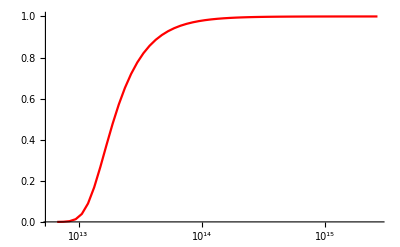

```mathematica
PlotNIntegrate=ListLogLinearPlot[λFinalCDFNorm,PlotStyle->Red,Joined->True]
```

```mathematica
LigoGravitonData=Import["/Users/stshammi/temp/graviton_mass_bound/ligo-graviton.csv","CSV"]
```

{{6.04×10^12,0.0131255},{7.08×10^12,0.0330231},{7.98×10^12,0.0614536},{8.64×10^12,0.086928},{9.36×10^12,0.11085},{1.01×10^13,0.134616},{1.07×10^13,0.15768},{1.13×10^13,0.184191},{1.19×10^13,0.217315},{1.25×10^13,0.25342},{1.32×10^13,0.28743},{1.39×10^13,0.318877},{1.47×10^13,0.349393},{1.55×10^13,0.378046},{1.63×10^13,0.404137},{1.72×10^13,0.429064},{1.82×10^13,0.45469},{1.92×10^13,0.479384},{2.02×10^13,0.504078},{2.13×10^13,0.528539},{2.25×10^13,0.553466},{2.37×10^13,0.576995},{2.5×10^13,0.59936},{2.64×10^13,0.620561},{2.78×10^13,0.64541},{3.01×10^13,0.671816},{3.26×10^13,0.695117},{3.53×10^13,0.715313},{3.82×10^13,0.736129},{4.14×10^13,0.756325},{4.54×10^13,0.778308},{4.99×10^13,0.800447},{5.4×10^13,0.820642},{5.93×10^13,0.840763},{6.68×10^13,0.860669},{7.83×10^13,0.881295},{9.56×10^13,0.901154},{1.21×10^14,0.923082},{1.6×10^14,0.941206},{2.15×10^14,0.955818},{2.88×10^14,0.966449},{3.86×10^14,0.975471},{5.22×10^14,0.985878},{6.02×10^14,0.993881},{7.69×10^14,0.993942},{1.03×10^15,0.996104},{1.38×10^15,0.997519},{1.85×10^15,0.998849},{2.48×10^15,1.00009}}

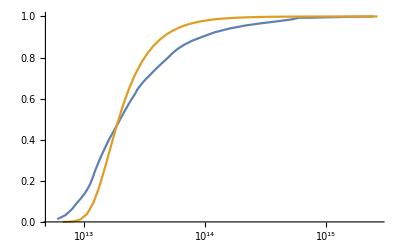

```mathematica
PlotLigoVSNIntegrate=ListLogLinearPlot[{LigoGravitonData,λFinalCDFNorm},PlotRange->All,Joined->True]
```

```mathematica
λFinalCDFNormInterp=Interpolation[λFinalCDFNorm]
```

InterpolatingFunction[…]

```mathematica
λInterpLigo=Interpolation[LigoGravitonData]
```

InterpolatingFunction[…]

```mathematica
FindRoot[λInterpLigo[x]==0.1,{x,10^13}] (*90% CL bound from Ligo*)
```

{x→9.02432×10^12}

```mathematica
FindRoot[λFinalCDFNormInterp[x]==0.1,{x,10^13}] (*90% CL bound from Nintegrate*)
```

{x→1.216×10^13}

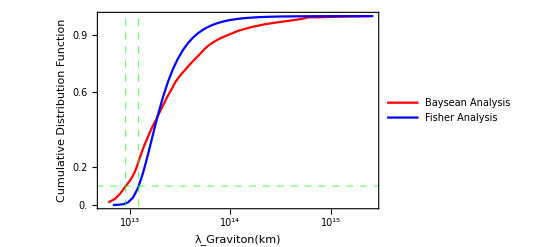

```mathematica
GraphExport=ListLogLinearPlot[{LigoGravitonData,λFinalCDFNorm},Joined->True,PlotRange->All,PlotStyle->{Red,Blue},GridLines->{{9.022142209468531*^12,1.216004814856395*^13},{0.1}},GridLinesStyle->Directive[Green, Dashed],PlotLegends->{Placed[LineLegend[{"Baysean Analysis ","Fisher Analysis"},LabelStyle->{Orange,FontSize->10},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{0.8,0.8}]},Frame->True,FrameLabel->{Style["λ_Graviton(km)",14],Style["Cumulative Distribution Function",12]},LabelStyle->{Purple,FontSize->10},FrameTicks->{{10^13//N,10^14//N,10^15//N},{0.0,0.1,0.2,0.4,0.6,0.8,0.9,1}}]
```

```mathematica
Export[NotebookDirectory[]<>"graviton.pdf",GraphExport,ImageResolution->2000]
```

/Users/stshammi/temp/graviton_mass_bound/graviton.pdf